```mathematica
(*define Fitness function*)
genNum=25;
strtBrd=SparseArray[{15,15}->1,{30,30}];

U=Normalize[#*(genNum-#+2.)&/@Range[genNum+1]];
fitness[dna_]:=-curveMatch[U,mass/@evolveTrace[dna,genNum][strtBrd]]

V=900*#/Max[#]&[#*(genNum-#+2.)&/@Range[genNum+1]];
V=900.Range[genNum+1]/(genNum+1);
fitness[dna_]:=-(V-#).(V-#)&[mass/@evolveTrace[dna,genNum][strtBrd]]
```

```mathematica
(*initial population*)
```

```mathematica
randDNA:=RandomInteger[1,512];
population=Table[randDNA,{popSize}];
```

```mathematica
popSize=12;
familySize=10;
mutN=50;
generations=200;
evoluationTrace=Reap[Do[
children=Flatten[Table[mutate[i,mutN],{familySize},{i,population}],1];
sortedPopulation=Sort[{fitness[#],#}&/@Join[children,population],First@#1>First@#2&];
Sow[sortedPopulation[[1]]];
newPopulation=#2&@@@sortedPopulation[[1;;popSize]];
population=newPopulation;,{generations}]][[2,1]];
```

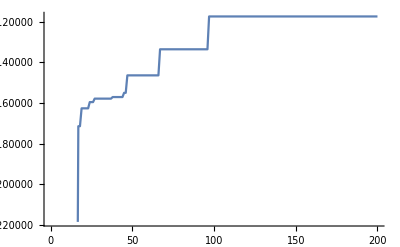

```mathematica
#1&@@@evoluationTrace//ListLinePlot
```

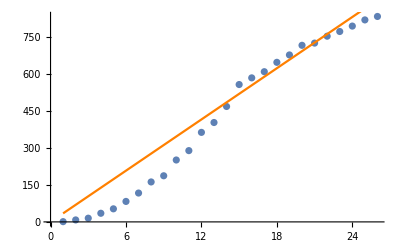

```mathematica
gen=-110;
Show[ListPlot[mass/@evolveTrace[evoluationTrace[[gen,2]],genNum][strtBrd]],ListLinePlot[V,PlotStyle->Orange]]
visulaiseTrace[evolveTrace[evoluationTrace[[gen,2]],genNum][strtBrd]]
```